## Energies

```mathematica
imtext=15;
sectext=20;
```

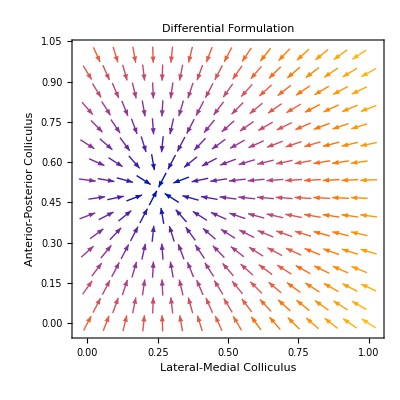

```mathematica
VectorPlot[{-x+0.25,-y+0.5},{x,0,1},{y,0,1}, PlotLabel->Style["Differential Formulation", "Section", sectext],
FrameLabel->{Style["Lateral-Medial Colliculus", Bold, imtext],Style["Anterior-Posterior Colliculus", Bold, imtext]},
Epilog->Inset[Graphics[{EdgeForm[Thick], White, Rectangle[{0,0},{L,L}], Green, Rectangle[{0.2 * L,0.45 * L},{0.3*L,0.55*L}], Black,Text["Retina", {0.5 * L, 0.8 * L}]}], {0.8, 0.8}, {0.0, 0.0},0.2]]
```

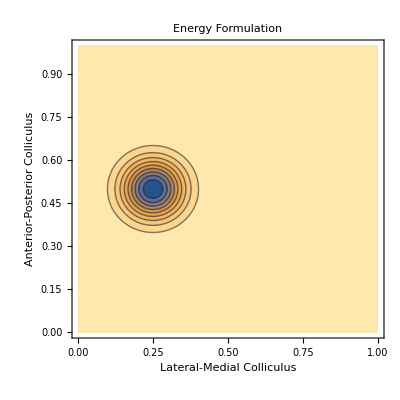

```mathematica
L=0.1;Show[

ContourPlot[{-Exp[-(x-0.25)^2/0.01]*Exp[-(y-0.5)^2/0.01]},{x,0,1},{y,0,1}, 
PlotRange->{-1,0},
PlotLabel->Style["Energy Formulation", "Section", sectext]],

FrameLabel->{Style["Lateral-Medial Colliculus", Bold, imtext],Style["Anterior-Posterior Colliculus", Bold, imtext]},Epilog->Inset[Graphics[{EdgeForm[Thick], White, Rectangle[{0,0},{L,L}], Green, Rectangle[{0.2 * L,0.45 * L},{0.3*L,0.55*L}],  Black,Text["Retina", {0.5 * L, 0.8 * L}]}], {0.8, 0.8}, {0.0, 0.0},0.2]

]
```

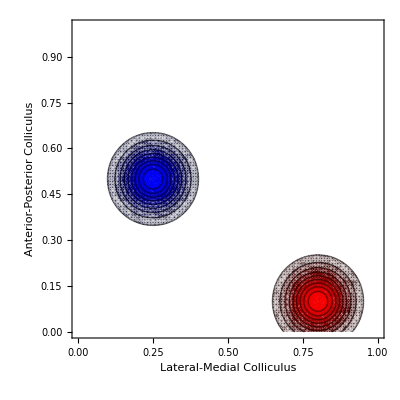

```mathematica
L=0.1;Show[

ContourPlot[{Exp[-(x-0.8)^2/0.01]*Exp[-(y-0.1)^2/0.01]},{x,0,1},{y,0,1},
ColorFunction->(RGBColor[#,0,0,#]&),
PlotRange->{0,1}],

ContourPlot[{Exp[-(x-0.25)^2/0.01]*Exp[-(y-0.5)^2/0.01]},{x,0,1},{y,0,1}, 
PlotRange->{0,1},
ColorFunction->(RGBColor[0,0,#,#]&),
PlotLabel->"Energy Formulation"],

FrameLabel->{"Lateral-Medial Colliculus", "Anterior-Posterior Colliculus"},Epilog->Inset[Graphics[{EdgeForm[Thick], White, Rectangle[{0,0},{L,L}], Blue, Rectangle[{0.2 * L,0.45 * L},{0.3*L,0.55*L}], Red, Rectangle[{0.8 * L,0.05 * L},{0.9*L,0.15*L}], Black,Text["Retina", {0.5 * L, 0.8 * L}]}], {0.8, 0.8}, {0.0, 0.0},0.2]

]
```

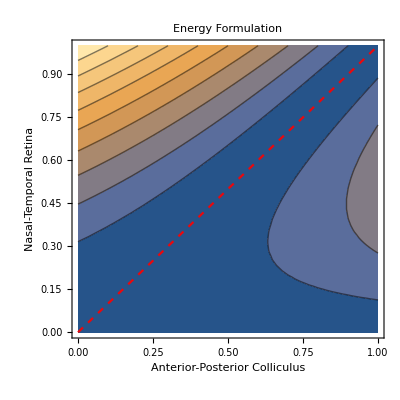

```mathematica
Show[
ContourPlot[Abs[-y*x+y^2],{x,0.0,1},{y,0.0,1},PlotRange->All, PlotLabel->Style["Energy Formulation", "Section", sectext]],

ContourPlot[y==x,{x,0.0,2},{y,0.0,1},PlotRange->All,ContourStyle->{Opacity[0.9],Directive[Red,Dashed,Bold]}, PlotLegends->Automatic],

FrameLabel->{Style["Anterior-Posterior Colliculus", Bold,imtext],Style[ "Nasal-Temporal Retina", Bold,imtext]}
]
```

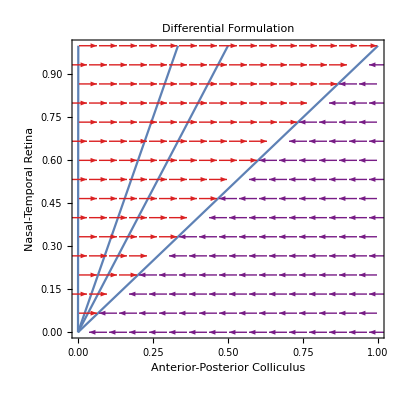

```mathematica
Show[Plot[Table[i x,{i, {1000, 3, 2, 1}}],{x,0,1},PlotRange->{0,1},AspectRatio->1,Frame->True,FrameLabel->{Style["Anterior-Posterior Colliculus", Bold, imtext], Style["Nasal-Temporal Retina", Bold, imtext]},PlotLabel->Style["Differential Formulation", "Section", sectext]],VectorPlot[{(-x+y),0},{x,0,1},{y,0,1}, VectorColorFunction->(ColorData["Rainbow", Sign[#3]]&)]]
```

## Descent Methods

```mathematica
rose[x_,y_]:=(1-x)^2+100(y-x^2)^2
test[x_,y_]:=1-Exp[-(x-2)^2-(y-0.4)^2]-Exp[-(x-0.1)^2-(y+0.2)^2]-Exp[-(x+0.5)^2-(y-0.7)^2]
gd[x_,y_]:={-2 (1-x)-400 x (-x^2+y),200 (-x^2+y)}
gdtest[x_,y_]:={2 ⅇ^(-(-2+x)^2-(-0.4+y)^2) (-2+x)+2 ⅇ^(-(-0.1+x)^2-(0.2+y)^2) (-0.1+x)+2 ⅇ^(-(0.5+x)^2-(-0.7+y)^2) (0.5+x),2 ⅇ^(-(0.5+x)^2-(-0.7+y)^2) (-0.7+y)+2 ⅇ^(-(-2+x)^2-(-0.4+y)^2) (-0.4+y)+2 ⅇ^(-(-0.1+x)^2-(0.2+y)^2) (0.2+y)}
```

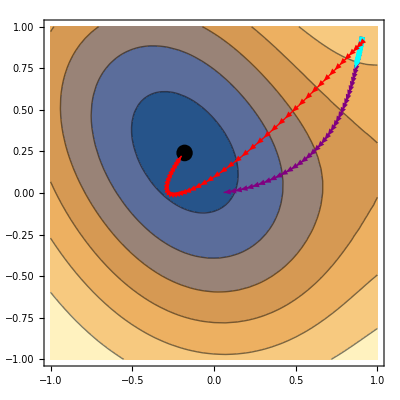

```mathematica
eta = 0.005;
alpha=0.9;
beta=0.999;
x0=0.9;
y0=0.9;
T=50;



GDvec=Table[{0,0},{i,1,T}];
GDpos=Table[{0,0},{i,1,T}];
GDpos[[1,1]]=x0;
GDpos[[1,2]]=y0;
For[i=2,i≤T,i++,
GDvec[[i]]=eta*gdtest[GDpos[[i-1,1]], GDpos[[i-1,2]]];
GDpos[[i]]=GDpos[[i-1]]-GDvec[[i-1]] ;
]

MOMvec=Table[{0,0},{i,1,T}];
MOMpos=Table[{0,0},{i,1,T}];
MOMpos[[1,1]]=x0;
MOMpos[[1,2]]=y0;
For[i=2,i≤T,i++,
MOMvec[[i]]=alpha*MOMvec[[i-1]]-eta*gdtest[MOMpos[[i-1,1]], MOMpos[[i-1,2]]];
MOMpos[[i]]=MOMpos[[i-1]]+MOMvec[[i-1]] ;
]

u=Table[{0,0},{i,1,T}];
v=Table[{0,0},{i,1,T}];
ADAMvec=Table[{0,0},{i,1,T}];
ADAMpos=Table[{0,0},{i,1,T}];
ADAMpos[[1,1]]=x0;
ADAMpos[[1,2]]=y0;
For[i=2,i≤T,i++,
u[[i]]=alpha*u[[i-1]]+(1-alpha)*gdtest[ADAMpos[[i-1,1]], ADAMpos[[i-1,2]]];
v[[i]]=beta*v[[i-1]]+(1-beta)*gdtest[ADAMpos[[i-1,1]], ADAMpos[[i-1,2]]]^2;
ADAMvec[[i]]=eta*u[[i]]/(1+alpha^i)/(Sqrt[v[[i]]/(1+beta^i)]+10^-7);
ADAMpos[[i]]=ADAMpos[[i-1]]-ADAMvec[[i-1]] ;
]

ContourPlot[test[x,y],{x,-1,1},{y,-1,1},

Epilog->Flatten[{
{Black, Disk[{x,y},0.05]/.Minimize[test[x,y],{x,y}][[2]]},
Table[{Purple,Arrowheads[0.02], Arrow[{MOMpos[[i-1]], MOMpos[[i]]}]},{i,2,T}],
Table[{Cyan,Arrowheads[0.02], Arrow[{GDpos[[i-1]], GDpos[[i]]}]},{i,2,T}],
Table[{Red,Arrowheads[0.02], Arrow[{ADAMpos[[i-1]], ADAMpos[[i]]}]},{i,2,T}]
}]
]
```

```mathematica
Minimize[test[x,y],{x,y}]
```

{-0.500801,{x→-0.183143,y→0.243813}}

```mathematica
{1,4}^2
```

{1,16}

```mathematica
Plot3D[1-Exp[-(x-2)^2-(y-0.4)^2]-Exp[-(x-0.1)^2-(y+0.2)^2]-Exp[-(x+0.5)^2-(y-0.7)^2],{x,-1,1},{y,-1,1},ColorFunction->"Heat"]
```

-Graphics3D-

## Receptive and Projective Field

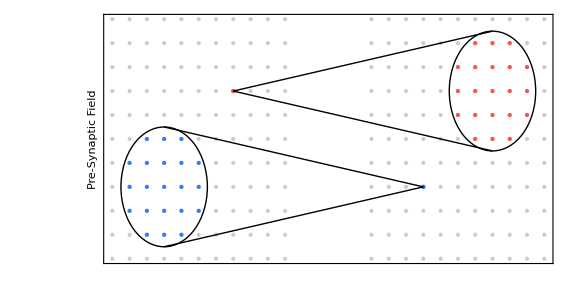

```mathematica
sep=1.5;
grid=0.1;
radius=0.25;
presynapticgrid=Flatten[Table[{i,j},{i,0,1,grid},{j,0,1,grid}],1];
postsynapticgrid=Flatten[Table[{i+sep,j},{i,0,1,grid},{j,0,1,grid}],1];

prenode={{0.7,0.7}};
projectivefield=Select[postsynapticgrid, Sqrt[(#[[1]]-sep-prenode[[1]][[1]])^2 + (#[[2]]-prenode[[1]][[2]])^2]<radius&];

postnode={{sep+0.3,0.3}};
receptivefield=Select[presynapticgrid, Sqrt[(#[[1]]+sep-postnode[[1]][[1]])^2 + (#[[2]]-postnode[[1]][[2]])^2]<radius&];

ListPlot[{presynapticgrid, postsynapticgrid, prenode,postnode, projectivefield,receptivefield},

PlotStyle->
{{Black, PointSize[Large], Opacity[0.2]}, 
{Black, PointSize[Large], Opacity[0.2]}, 
{RGBColor[1.,0.31,0.31], PointSize[Large]}, 
{RGBColor[0.15,0.51,1.], PointSize[Large]}, 
{RGBColor[1.,0.31,0.31], PointSize[Large]}, 
{RGBColor[0.15,0.51,1.], PointSize[Large]}}, 

Epilog->
{Circle[{prenode[[1]][[1]]+sep,prenode[[1]][[2]]},radius], 
Circle[{postnode[[1]][[1]]-sep,postnode[[1]][[2]]},radius], 
Line[{{prenode[[1]][[1]],prenode[[1]][[2]]},{prenode[[1]][[1]]+sep,prenode[[1]][[2]]+radius}}],
Line[{{prenode[[1]][[1]],prenode[[1]][[2]]},{prenode[[1]][[1]]+sep,prenode[[1]][[2]]-radius}}],
Line[{{postnode[[1]][[1]],postnode[[1]][[2]]},{postnode[[1]][[1]]-sep,postnode[[1]][[2]]+radius}}],
Line[{{postnode[[1]][[1]],postnode[[1]][[2]]},{postnode[[1]][[1]]-sep,postnode[[1]][[2]]-radius}}]}
,
FrameLabel->{{Style["Pre-Synaptic Field",Bold,Gray,16],Style["Post-Synaptic Field", Bold,Gray,16]},{"", ""}},

AspectRatio->0.5, Ticks->None, Axes->None,Frame->True,FrameTicks->None, ImageSize->Large]
```